# HW 10 - AstroDynamics

## Daniel George

## Q2 b)

## Reading data from the tabular dump files with B = 0:

```mathematica
B0t=Reap[Do[str=OpenRead["A:\\HW10\\B=0\\Blast_B1.00"<>If[i<10,"0",""]<>ToString[i]<>".tab"];
Skip[str,Record,6];
Sow[ReadList[str,Table[Number,12],60006,RecordSeparators->{"\t","\n"}]];
Close[str],{i,0,10}]]⟦2,1⟧;
```

## Defining column names

```mathematica
iZone=1;jZone=2; x1=3;x2=4;d=5; V1=6;V2=7;V3=8;p=9;B1c=10;B2c=11;B3c=12;
```

## Plots

### Colormap of pressure at successive time steps

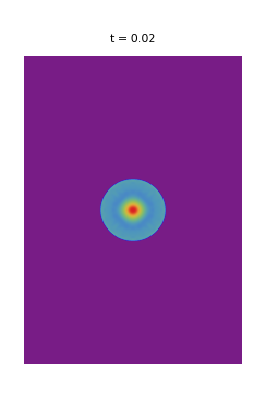
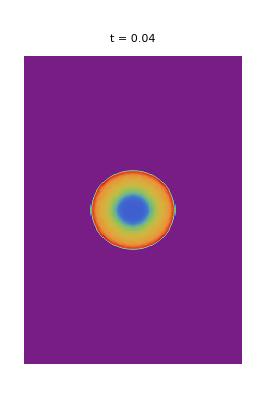
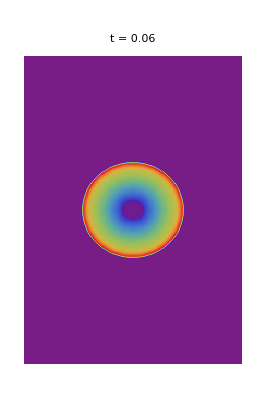
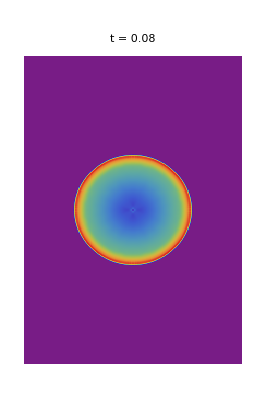
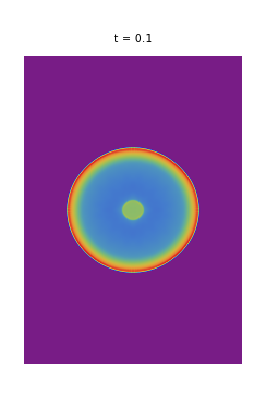
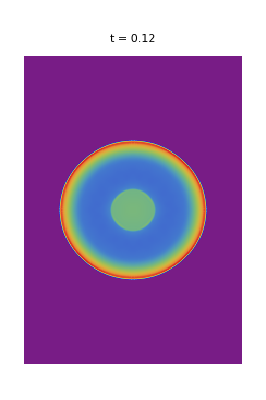
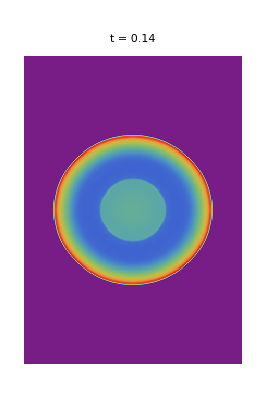
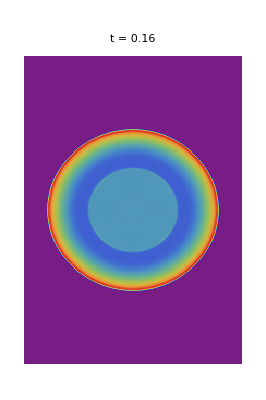

```mathematica
Table[ArrayPlot[Reverse@Partition[B0t⟦i⟧⟦All,p⟧,200],ImageSize->Tiny,ColorFunction->"Rainbow",PlotLabel->"t = "<>ToString[.02(i-1)]],{i,2,11}]//Row
```

### Colormap of density at successive time steps

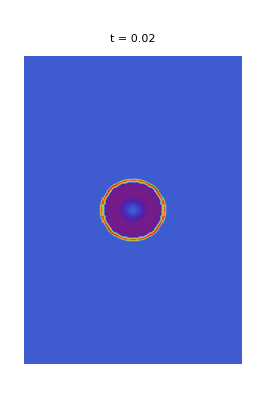
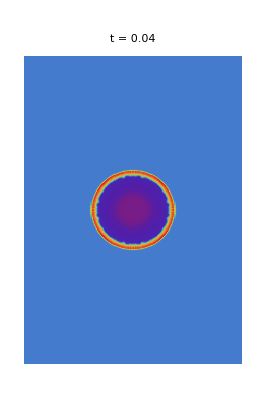
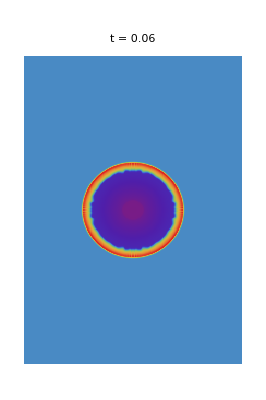
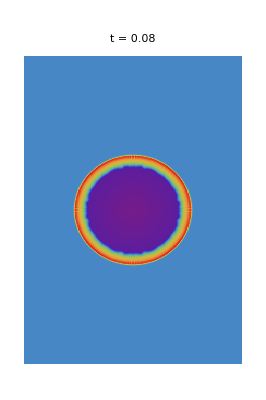
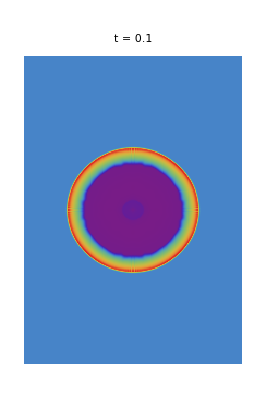
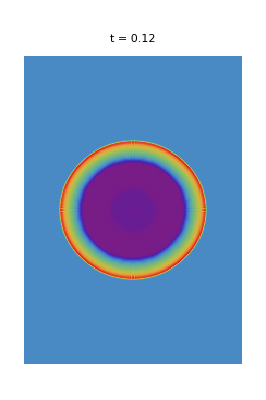
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Table[ArrayPlot[Reverse@Partition[B0t⟦i⟧⟦All,d⟧,200],ImageSize->Tiny,ColorFunction->"Rainbow",PlotLabel->"t = "<>ToString[.02(i-1)]],{i,2,11}]//Row
```

## Radial averages (width of bins = width of zones)

### Grouping zones by radial distance

```mathematica
grid=GatherBy[Tuples[{Range[200],Range[300]}],Floor [Norm [#-{100.5,150.5}]]&];
```

### Averaging density over each bin

Finding density at each zone:

```mathematica
d0=Table[Transpose[Partition[B0t⟦i⟧⟦All,d⟧,200]],{i,1,11}];
```

Now averaging it over each radial group of zones:

```mathematica
d0Av=Table[Reverse[Mean/@(Extract[d0⟦i⟧,#]&/@grid)],{i,11}];
```

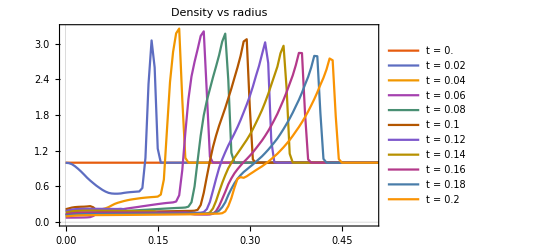

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[d0Av⟦i⟧]-1}],d0Av⟦i⟧}],{i,11}],PlotRange->{{0,100*.005},All},Frame->True,PlotTheme->{"Scientific"},PlotLegends->Table["t = "<>ToString[.02i],{i,0,10}],PlotLabel->"Density vs radius"]
```

### Averaging radial velocity over each bin

Finding radial component of velocity at each zone:

```mathematica
Vr0=Table[(#⟦1⟧*#⟦3⟧+#⟦2⟧*#⟦4⟧)/Sqrt[#⟦3⟧^2+#⟦4⟧^2]&[Transpose[Partition[B0t⟦i⟧⟦All,#⟧,200]]&/@{V1,V2,x1,x2}],{i,11}];
```

Now averaging it over each radial group of zones:

```mathematica
Vr0Av=Table[Reverse[Mean/@(Extract[Vr0⟦i⟧,#]&/@grid)],{i,11}];
```

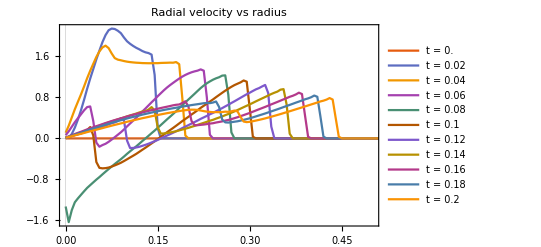

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[Vr0Av⟦i⟧]-1}],Vr0Av⟦i⟧}],{i,11}],PlotRange->{{0,100*.005},All},Frame->True,PlotTheme->{"Scientific"},PlotLegends->Table["t = "<>ToString[.02i],{i,0,10}],PlotLabel->"Radial velocity vs radius"]
```

### Averaging pressure over each bin

Finding pressure at each zone:

```mathematica
p0=Table[Transpose[Partition[B0t⟦i⟧⟦All,p⟧,200]],{i,1,11}];
```

Now averaging it over each radial group of zones:

```mathematica
p0Av=Table[Reverse[Mean/@(Extract[p0⟦i⟧,#]&/@grid)],{i,11}];
```

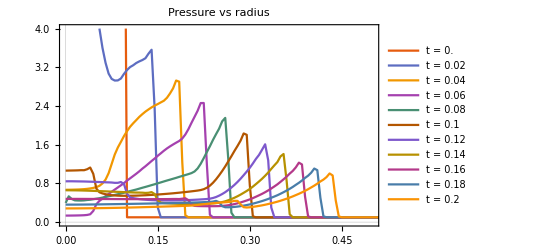

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[p0Av⟦i⟧]-1}],p0Av⟦i⟧}],{i,11}],PlotTheme->{"Scientific"},PlotRange->{{0,100*.005},{0,4}},Frame->True,PlotLegends->Table["t = "<>ToString[.02i],{i,0,10}],PlotLabel->"Pressure vs radius"]
```

## Finding shock front position from pressure profile

We can find the shock front position by calculating the location of the first maxima which we encounter as we move from the edges to the center.

```mathematica
sh0=Transpose[{Range[0,.2,.02],.005((FindPeaks[#,0,.05,-∞]&/@p0Av)⟦All,-1,1⟧-1)}];sh0⟦1,2⟧=20*.005;
```

### Analytic fit

The Sedov blast is expected to scale as t^(2/5) with time. Therefore we can try fitting this function to our calculated values:

```mathematica
fsh0[t_]=Fit[sh0⟦2;;-1⟧,{1,t^(2/5)},t]
```

-0.0742247+0.941323 t^(2/5)

### Plotting radial position of the shock front vs time

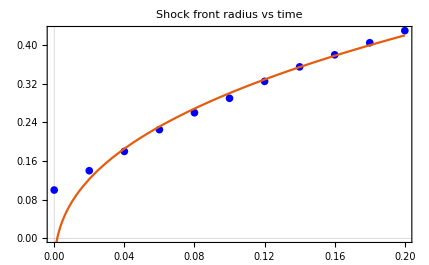

```mathematica
Show[ListPlot[sh0,Frame->True,PlotStyle->Blue,PlotTheme->{"Scientific"},PlotLabel->"Shock front radius vs time"],Plot[fsh0[t],{t,0,.2},PlotTheme->{"Scientific"}]]
```

The red line is the computed value of shock front position. The blue line is the analytic fit. We can see that after a small amount of time, the calculated shock front radius matches the analytic fit as expected.

## Q2 c)

## Reading data from the tabular dump files with B = 1:

```mathematica
B1t=Reap[Do[str=OpenRead["A:\\HW10\\B=1\\Blast_B1.00"<>If[i<10,"0",""]<>ToString[i]<>".tab"];
Skip[str,Record,6];
Sow[ReadList[str,Table[Number,12],60006,RecordSeparators->{"\t","\n"}]];
Close[str],{i,0,10}]]⟦2,1⟧;
```

## Plots

### Colormap of pressure at successive time steps

```mathematica
Table[ArrayPlot[Reverse@Partition[B1t⟦i⟧⟦All,p⟧,200],ImageSize->Tiny,ColorFunction->"Rainbow", PlotLabel->"t = "<>ToString[.02(i-1)]],{i,2,11}]//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

### Colormap of density at successive time steps

```mathematica
Table[ArrayPlot[Reverse@Partition[B1t⟦i⟧⟦All,d⟧,200],ImageSize->Tiny,ColorFunction->"Rainbow", PlotLabel->"t = "<>ToString[.02(i-1)]],{i,2,11}]//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

You can observe that the shock is not spherically symmetric. The rate of expansion of minimum radius of the shock front is comparable to the hydrodynamic case. The maximum and minimum radius of the shock front lies along the x = -y line and the x = y line respectively.

## Properties (in cgs units)

### Ambient plasma β value

```mathematica
Pamb=0.1;(*Ambient pressure*)
B=1.;(*Magnetic field strength*)
```

```mathematica
β=Pamb/(B^2/(8Pi))
```

2.51327

### Alfven speed

```mathematica
ρ0=1.;
```

The Alfven speed (Va) is given by:

```mathematica
Va=B/Sqrt[4Pi ρ0]
```

0.282095

### Magnetosonic speed

```mathematica
Vs=0.4082482905 ;(*Speed of sound from athinput.blast_B1*)
```

Speeds of the fast and slow MHD waves are functions of angle θ given by the following formulae:

√(1/2 (√((Va^2+Vs^2)^2±4 Va^2 Vs^2 Cos[θ-π/4]^2)+Va^2+Vs^2))

```mathematica
VmFast[θ_]:=Sqrt[1/2(Va^2+Vs^2+Sqrt[(Va^2+Vs^2)^2-4Va^2Vs^2Cos[θ-Pi/4]^2])];
VmSlow[θ_]:=Sqrt[1/2(Va^2+Vs^2-Sqrt[(Va^2+Vs^2)^2-4Va^2Vs^2Cos[θ-Pi/4]^2])];
```

### Plots of different speeds vs angle

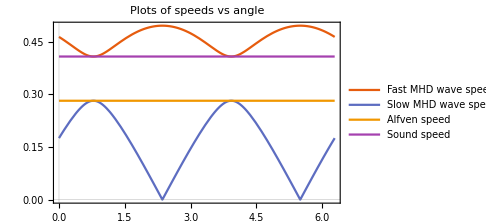
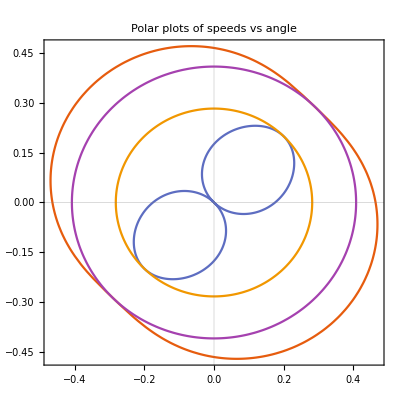

```mathematica
{Plot[{VmFast[θ],VmSlow[θ],Va,Vs},{θ,0,2Pi},Frame->True,ImageSize->Medium,PlotLegends->Placed[{"Fast MHD wave speed","Slow MHD wave speed","Alfven speed","Sound speed"},Below],PlotTheme->{"Scientific"},PlotLabel->"Plots of speeds vs angle"],PolarPlot[{VmFast[θ],VmSlow[θ],Va,Vs},{θ,0,2Pi},PlotLabel->"Polar plots of speeds vs angle",Frame->True,ImageSize->{250},PlotTheme->{"Scientific"}]}//Row
```

Therefore the speed of the shock will be maximum perpendicular to the magnetic field i.e. along 135° angle (x = -y line) since the dominant fast MHD wave has maximum speed in this direction. Similarly the shock speed along 45° angle (x = y line) will be minimum. Thus the Mach number will be maximum along 135° angle and minimum along 45° angle (see below).

### Colormap of Mach number at successive time steps

Mach number at each zone = magnitude of velocity divided by sound speed in that zone:

```mathematica
Mach=Table[(#⟦1⟧^2+#⟦2⟧^2)/Sqrt[5/3#⟦3⟧/#⟦4⟧]&[Transpose[Partition[B1t⟦i⟧⟦All,#⟧,200]]&/@{V1,V2,p,d}],{i,1,11}];
```

```mathematica
Table[ArrayPlot[Reverse@Transpose[Mach⟦i⟧],ImageSize->Tiny,AspectRatio->3/2, ColorFunction->"Rainbow",PlotLabel->"t = "<>ToString[.02(i-1)]],{i,2,11}]//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Radial averages (width of bins = width of zones)

### Averaging density over each bin

Finding density at each zone:

```mathematica
d1=Table[Transpose[Partition[B1t⟦i⟧⟦All,d⟧,200]],{i,1,11}];
```

Now averaging it over each radial group of zones:

```mathematica
d1Av=Table[Reverse[Mean/@(Extract[d1⟦i⟧,#]&/@grid)],{i,11}];
```

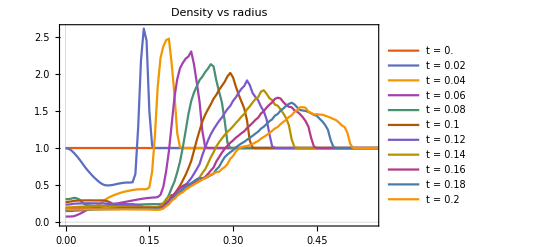

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[d1Av⟦i⟧]-1}],d1Av⟦i⟧}],{i,11}],PlotTheme->{"Scientific"},PlotRange->{{0,110*.005},All},Frame->True,PlotLegends->Table["t = "<>ToString[.02i],{i,0,10}],PlotLabel->"Density vs radius"]
```

### Averaging radial velocity over each bin

Finding radial component of velocity at each zone:

```mathematica
Vr1=Table[(#⟦1⟧*#⟦3⟧+#⟦2⟧*#⟦4⟧)/Sqrt[#⟦3⟧^2+#⟦4⟧^2]&[Transpose[Partition[B1t⟦i⟧⟦All,#⟧,200]]&/@{V1,V2,x1,x2}],{i,11}];
```

Now averaging it over each radial group of zones:

```mathematica
Vr1Av=Table[Reverse[Mean/@(Extract[Vr1⟦i⟧,#]&/@grid)],{i,11}];
```

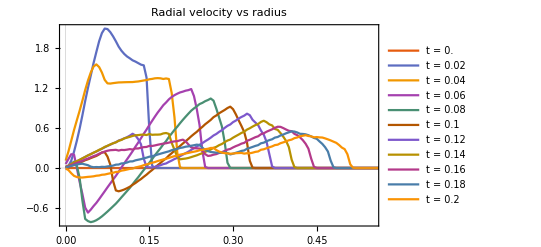

```mathematica
ListLinePlot[Table[Transpose[{Table[j*.005,{j,0,Length[Vr1Av⟦i⟧]-1}],Vr1Av⟦i⟧}],{i,11}],PlotRange->{{0,110*.005},All},Frame->True,PlotLegends->Table["t = "<>ToString[.02i],{i,0,10}],PlotTheme->{"Scientific"},PlotLabel->"Radial velocity vs radius"]
```

## Finding maximum and minimum radius of shock front

Since the shock is elliptical and symmetric about the x = y line, we can assume that the maximum and minimum radius of the shock front will be either on the line x = y or on the line x = -y.

### Shock front along 45° angle (x = y line)

Finding zones along the 45° line:

```mathematica
grid45=Table[{i,i+50},{i,1,200}];
```

Finding pressure at different values of radial distance along 45° line:

```mathematica
p1Av45=(#⟦All,100;;1;;-1⟧+#⟦All,101;;200⟧)/2&[Table[(Extract[Transpose[Partition[B1t⟦i⟧⟦All,p⟧,200]],grid45]),{i,11}]];
```

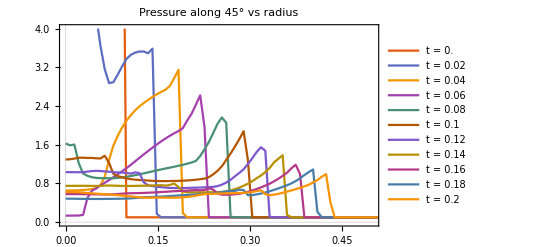

```mathematica
ListLinePlot[Table[Transpose[{Table[.005*Sqrt[2]j,{j,0,Length[p1Av45⟦i⟧]-1}],p1Av45⟦i⟧}],{i,11}],PlotRange->{{0,100*.005},{0,4}},Frame->True,PlotTheme->{"Scientific"},PlotLegends->Table["t = "<>ToString[.02i],{i,0,11}],PlotLabel->"Pressure along 45° vs radius"]
```

Calculating position of shock front by finding the first peak that we encounter while moving from the edges to the center:

```mathematica
sh45=Transpose[{Range[0,.2,.02],.005*Sqrt[2]((FindPeaks[#,0,.05,-∞]&/@p1Av45)⟦All,-1,1⟧-1)}];sh45⟦1,2⟧=.1;
```

### Shock front along 135° angle (x = -y line)

Finding zones along the 135° line:

```mathematica
grid135=Table[{i,251-i},{i,1,200}];
```

Finding pressure at different values of radial distance along 135° line:

```mathematica
p1Av135=(#⟦All,100;;1;;-1⟧+#⟦All,101;;200⟧)/2&[Table[(Extract[Transpose[Partition[B1t⟦i⟧⟦All,p⟧,200]],grid135]),{i,11}]];
```

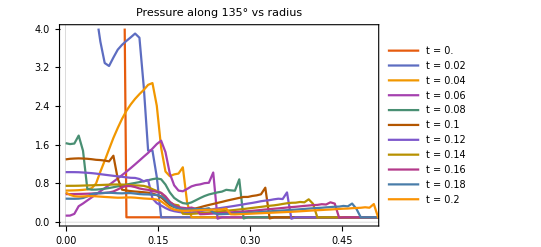

```mathematica
ListLinePlot[Table[Transpose[{Table[.005*Sqrt[2]j,{j,0,Length[p1Av135⟦i⟧]-1}],p1Av135⟦i⟧}],{i,11}],PlotRange->{{0,100*.005},{0,4}},Frame->True,PlotLegends->Table["t = "<>ToString[.02i],{i,0,11}],PlotLabel->"Pressure along 135° vs radius",PlotTheme->{"Scientific"}]
```

Calculating position of shock front by finding the first peak that we encounter while moving from the edges to the center:

```mathematica
sh135=Transpose[{Range[0,.2,.02],.005*Sqrt[2]((FindPeaks[#,0,.05,-∞]&/@p1Av135)⟦All,-1,1⟧-1)}];sh135⟦1,2⟧=.1;
```

### Plots of the maximum and minimum radius of the shock front vs time

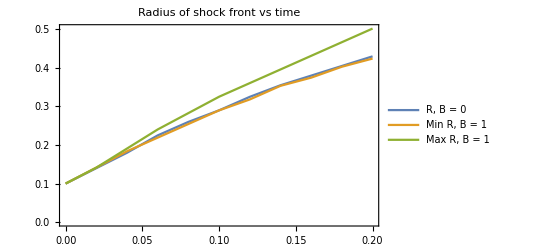

```mathematica
Show[ListLinePlot[{sh0,sh45,sh135},Frame->True,PlotLegends->{"R,  B = 0","Min R, B = 1","Max R, B = 1"},PlotLabel->"Radius of shock front vs time"]]
```

It can be observed that the hydrodynamic shock radius (which scales as t^(2/5)) closely matches the minimum radius of the MHD shock front. This is because along the magnetic field (45° angle) the fast MHD wave which is dominant has speed equal to the sound speed. Perpendicular to the magnetic field (135° angle) the fast MHD wave speed is greater than the sound speed (see plots of speeds in the previous section) therefore the shock front radius scales faster than the hydrodynamic case.